```mathematica
GetData[trajectories_]:=Module[{bodiesall,directorsall,subunits,directors,bodyparticles,central,north,east,b1,b2,b3,linkers},
bodiesall={};
directorsall={};
Monitor[Do[
particles=trajectories[[1+21*4*(f-1);;21*4*f]];
subunits={};
directors={};
Do[
bodyparticles=particles[[1+21*(i-1);;21*i]];
central=Select[bodyparticles,#[[5]]=="central"&][[1]][[2;;4]];
north=Mean[Map[#[[2;;4]]&,Select[bodyparticles,#[[5]]=="N1"||#[[5]]=="N2"||#[[5]]=="N3"||#[[5]]=="N4"&]]];
east=Mean[Map[#[[2;;4]]&,Select[bodyparticles,#[[5]]=="E1"||#[[5]]=="E2"||#[[5]]=="E3"||#[[5]]=="E4"&]]];

b1=(east-central)/Norm[east-central];
b2=(north-central)/Norm[north-central];
b3=Cross[b1,b2];
AppendTo[subunits,Polyhedron[{central+0.5*b2+0.5/Sqrt[2]*b3,central+0.5*b1+0.5/Sqrt[2]*b3,central-0.5*b2+0.5/Sqrt[2]*b3,central-0.5*b1+0.5/Sqrt[2]*b3,central+0.5*b2-0.5/Sqrt[2]*b3,central+0.5*b1-0.5/Sqrt[2]*b3,central-0.5*b2-0.5/Sqrt[2]*b3,central-0.5*b1-0.5/Sqrt[2]*b3},{{1,2,3,4},{5,6,7,8},{1,2,6,5},{2,3,7,6},{3,4,8,6},{4,1,5,8}}]];
AppendTo[directors,{b1,b2,b3}];
,{i,1,4}];
linkers=Map[Sphere[#[[2;;4]],0.5]&,Select[particles,#[[5]]=="linker"&]];
AppendTo[bodiesall,Join[subunits,linkers]];
AppendTo[directorsall,directors];
,{f,1,10000}],f];

{bodiesall,directorsall}
]
```

```mathematica
trajectories=Import[NotebookDirectory[]<>"TEST_OUTPUT/trajectories_w_0p00.txt","csv"][[2;;]];
```

```mathematica
{bodiesall,directorsall}=GetData[trajectories];
```

```mathematica
frames=Table[Graphics3D[bodiesall[[f]],PlotRange->{{0,5},{0,5},{0,5}}],{f,1,10000}];
```

```mathematica
Export[NotebookDirectory[]<>"TEST_OUTPUT/sim.gif",frames[[1;;50]],"DisplayDurations"->0.1]
```

/home/mwang/Documents/GFAs/GFAsFiniteT/test/TEST_OUTPUT/sim.gif

```mathematica
Manipulate[frames[[f]],{f,1,10000,1}]
```

Part::partd: Part specification frames[[1310]] is longer than depth of object.

```mathematica
ListPlot[Map[ArcCos[Dot[#[[1]][[2]],#[[2]][[2]]]]&,directorsall],Joined->True]
```

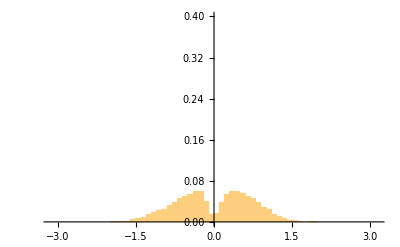

```mathematica
histogram=Show[Histogram[Map[ArcCos[Dot[#[[1]][[2]],#[[2]][[2]]]]*Sign[Dot[Cross[#[[1]][[2]],#[[2]][[2]]],#[[1]][[3]]]]&,directorsall],{0.1},"Probability"],PlotRange->{{-Pi,Pi},{0,0.4}},AxesOrigin->{0,0}]
```

```mathematica
p11n={0,1/2};
p11e={1/2,0};
p12w=RotationMatrix[θ12].{-1/2,0}+{1/2+x12,y12};
p12n=RotationMatrix[θ12].{0,1/2}+{1/2+x12,y12};
p21s=RotationMatrix[θ21].{0,-1/2}+{x21,1/2+y21};
p21e=RotationMatrix[θ21].{1/2,0}+{x21,1/2+y21};
p22s=RotationMatrix[θ22].{0,-1/2}+{1/2+x22,1/2+y22};
p22w=RotationMatrix[θ22].{-1/2,0}+{1/2+x22,1/2+y22};
```

```mathematica
pairs={p21s-p11n,p12w-p11e,p22w-p21e,p22s-p12n};
integrand=Exp[Sum[-1/2*k*Dot[Δ,Δ],{Δ,pairs}]]
```

ⅇ^(-1/2 k ((x12-Cos[θ12]/2)^2+(y12-Sin[θ12]/2)^2)-1/2 k ((y21-Cos[θ21]/2)^2+(x21+Sin[θ21]/2)^2)-1/2 k ((1/2-x21+x22-Cos[θ21]/2-Cos[θ22]/2)^2+(-y21+y22-Sin[θ21]/2-Sin[θ22]/2)^2)-1/2 k ((1/2-y12+y22-Cos[θ12]/2-Cos[θ22]/2)^2+(-x12+x22+Sin[θ12]/2+Sin[θ22]/2)^2))

```mathematica
step1=Integrate[integrand,{x12,-Infinity,Infinity},Assumptions->k>0]
step2=Integrate[step1,{y12,-Infinity,Infinity},Assumptions->k>0]
step3=Integrate[step2,{x21,-Infinity,Infinity},Assumptions->k>0]
step4=Integrate[step3,{y21,-Infinity,Infinity},Assumptions->k>0]
step5=Integrate[step4,{x22,-Infinity,Infinity},Assumptions->k>0]
step6=Integrate[step5,{y22,-Infinity,Infinity},Assumptions->k>0]
```

1/(√k)ⅇ^(-1/16 k (29/2-8 x21+16 x21^2+8 x22-16 x21 x22+12 x22^2-8 y12+16 y12^2+16 y21^2+8 y22-16 y12 y22-16 y21 y22+16 y22^2-8 Cos[θ22]+8 x21 Cos[θ22]-8 x22 Cos[θ22]+8 y12 Cos[θ22]-8 y22 Cos[θ22]+Cos[θ22]^2/2+4 Cos[θ21] (-1+2 x21-2 x22-2 y21+Cos[θ22])+4 x22 Sin[θ12]-8 y12 Sin[θ12]+8 x21 Sin[θ21]+8 y21 Sin[θ21]-8 y22 Sin[θ21]+4 x22 Sin[θ22]+8 y21 Sin[θ22]-8 y22 Sin[θ22]+2 Sin[θ12] Sin[θ22]+4 Sin[θ21] Sin[θ22]-Sin[θ22]^2/2-2 Cos[θ12] (2+2 x22-4 y12+4 y22-2 Cos[θ22]+Sin[θ12]+Sin[θ22]))) √π

1/k ⅇ^(-1/8 k (6-4 x21+8 x21^2+4 x22-8 x21 x22+6 x22^2+8 y21^2+2 y22-8 y21 y22+6 y22^2-(1+2 x22+2 y22) Cos[θ12]+(-2+4 x21-4 x22-4 y21) Cos[θ21]+Cos[θ12-θ22]+2 Cos[θ21-θ22]-3 Cos[θ22]+4 x21 Cos[θ22]-4 x22 Cos[θ22]-2 y22 Cos[θ22]-Sin[θ12]+2 x22 Sin[θ12]-2 y22 Sin[θ12]+4 x21 Sin[θ21]+4 y21 Sin[θ21]-4 y22 Sin[θ21]+Sin[θ12-θ22]+2 x22 Sin[θ22]+4 y21 Sin[θ22]-4 y22 Sin[θ22])) π

1/k^(3/2)ⅇ^(1/16 k ((-1-2 x22+Cos[θ21]+Cos[θ22]+Sin[θ21])^2-2 (6+4 x22+6 x22^2+8 y21^2+2 y22-8 y21 y22+6 y22^2-(1+2 x22+2 y22) Cos[θ12]-2 (1+2 x22+2 y21) Cos[θ21]+Cos[θ12-θ22]+2 Cos[θ21-θ22]-3 Cos[θ22]-4 x22 Cos[θ22]-2 y22 Cos[θ22]-Sin[θ12]+2 x22 Sin[θ12]-2 y22 Sin[θ12]+4 y21 Sin[θ21]-4 y22 Sin[θ21]+Sin[θ12-θ22]+2 x22 Sin[θ22]+4 y21 Sin[θ22]-4 y22 Sin[θ22]))) π^(3/2)

1/k^2 ⅇ^(-1/8 k (4+2 x22+4 x22^2+2 y22+4 y22^2-(1+2 x22+2 y22) Cos[θ12]-(1+2 x22+2 y22) Cos[θ21]+Cos[θ12-θ22]+Cos[θ21-θ22]-2 Cos[θ22]-2 x22 Cos[θ22]-2 y22 Cos[θ22]-Sin[θ12]+2 x22 Sin[θ12]-2 y22 Sin[θ12]+Sin[θ21]+2 x22 Sin[θ21]-2 y22 Sin[θ21]+Sin[θ12-θ22]-Sin[θ21-θ22]+2 x22 Sin[θ22]-2 y22 Sin[θ22])) π^2

1/k^(5/2)√2 ⅇ^(-1/32 k (12+8 y22+16 y22^2-2 (1+4 y22) Cos[θ12]-2 Cos[θ12-θ21]-2 Cos[θ21]-8 y22 Cos[θ21]+2 Cos[θ12-θ22]+2 Cos[θ21-θ22]-6 Cos[θ22]-8 y22 Cos[θ22]-6 Sin[θ12]-8 y22 Sin[θ12]+Sin[2 θ12]+2 Sin[θ21]-8 y22 Sin[θ21]+Sin[2 θ21]+2 Sin[θ12+θ21]+4 Sin[θ12-θ22]-4 Sin[θ21-θ22]-2 Sin[θ22]-8 y22 Sin[θ22]+Sin[2 θ22]+2 Sin[θ12+θ22]+2 Sin[θ21+θ22])) π^(5/2)

(2 ⅇ^(1/8 k (-2+Cos[θ12-θ21]+Cos[θ22]+Sin[θ12]-Sin[θ21]-Sin[θ12-θ22]+Sin[θ21-θ22])) π^3)/k^3

```mathematica
step6=(2 ⅇ^(1/8 k (-2+Cos[θ12-θ21]+Cos[θ22]+Sin[θ12]-Sin[θ21]-Sin[θ12-θ22]+Sin[θ21-θ22])) π^3)/k^3;
```

```mathematica
norm=NIntegrate[step6/.k->100,{θ21,-Pi/2,Pi/2},{θ22,-Pi/2,Pi/2},{θ12,-Pi/2,Pi/2}];
data=Table[{θ12,0.1*NIntegrate[step6/.k->100,{θ21,-Pi/2,Pi/2},{θ22,-Pi/2,Pi/2}]/norm},{θ12,-Pi/2,Pi/2,0.1}];
```

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.000150425 and 2.02598×10^-9 for the integral and error estimates.

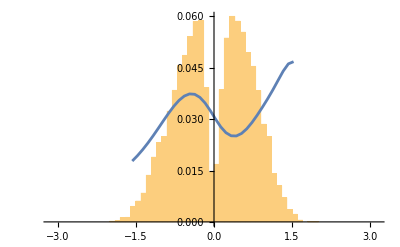

```mathematica
Show[histogram,ListPlot[data,Joined->True],PlotRange->{{-Pi,Pi},All}]
```